```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Spanish";
```

# Lenguaje Wolfram y el entorno de Mathematica

Por: José Alfredo de León

## Plan para hoy y mañana:

Hoy: vamos a ver para lo que se imaginan que se puede utilizar Mathematica, las herramientas básicas para empezar a usar el lenguaje de Wolfram y los cuadernos de Mathematica.

Mañana: lo que probablemente no sabían de Wolfram, algunas herramientas intermedias para sacarle jugo al lenguaje y al paradigma de la programación simbólica.

## Plan para hoy:

1. Introducción: sobre el lenguaje de Wolfram y el entorno Mathematica
2. Manos a la obra: vamos a aprender probando el lenguaje de Wolfram y leyendo documentación (la documentación de Wolfram es la mejor de todas las documentaciones que me ha tocado revisar)

## Introducción

#### Lenguaje de Wolfram (el lenguaje no se llama Mathematica)

Wolfram es otro lenguaje frecuentemente utilizado para hacer programación científica. Al igual que Python, Wolfram es un lenguaje interpretado y no compilado (como sí lo son C/C++, FORTRAN, etc). Este lenguaje es especialmente conocido por su paradigma de la programación simbólica. Recuerden la forma en que utilicé Python en los Jupyter Notebooks, especialmente en el último para mostrar el uso del módulo ‘JAquantum’; similar a esa forma de programar es el paradigma de Wolfram.

#### ¿Qué es Mathematica? La interfaz.

Wolfram Mathematica es un entorno para el lenguaje de Wolfram como Jupyter Notebook es un entorno para el lenguaje de Python, pero como Wolfram Mathematica es de paga podemos decir que es un Jupyter Notebook con mega esteroides. Tiene tantas herramientas que hasta se pueden escribir artículos científicos y hacer presentaciones con diapositivas. 

Esto significa que también se pueden hacer scripts de Wolfram (*.wls) y ejecutarlos afuera del entorno de Mathematica. Ya que Wolfram es de paga, el intérprete de Wolfram no viene instalado en sistemas operativos como Linux.

#### Usos de Wolfram:

1. Resolver operaciones matemáticas (desde lo más sencillo hasta cosas complicadas como manipular funciones especiales o calcular transformadas integrales).
2. Hacer rutinas para que Wolfram resuelve por uno los cálculos de proyectos de investigación.
2. Hacer machine learning.
3. Análisis de datos. 
4. Y mucho más... yo aún no alcanzo a dimensionar todo lo que se puede hacer con Wolfram.

## Manos a la obra

#### ¿Cómo ejecuto código Wolfram en Mathematica?

Shift + Enter a una celda que se encuentre en modo ‘input’ (esta celda se encuentra en modo ‘text’).

```mathematica
1+5
```

6

```mathematica
23*24
```

552

```mathematica
45/57
```

15/19

Hmm.. ¿y si quiero el valor numérico?

```mathematica
N[%]
```

0.789474

Acá aparecieron dos cosas del lenguaje Wolfram: la función N[], para obtener un valor numérico y ‘%’ para utilizar última salida del cuaderno (no necesariamente la de arriba).

También podemos hacer operaciones con símbolos:

```mathematica
a+b
```

a+b

```mathematica
a^2
```

a^2

Hack 1: Ctrl + 6 para poner un exponente

```mathematica
a^2
```

a^2

Hack 2: Ctrl + / para poner fracciones chulas

```mathematica
x/y
```

x/y

Asignación a una variable o símbolo:

```mathematica
s=1
```

1

```mathematica
p=2
```

2

Luego, al efectuar operaciones entre símbolos con valores asignados:

```mathematica
s+p
```

3

Naturalmente, de las primeras cosas que nos sugiere hacer la programación simbólica es probar funciones matemáticas de Wolfram para calcular límites, derivar (parcial y total), integrar, aplicar una transformada de Laplace o de Fourier, hacer una expansión en series, aplicar el operador gradiente, etc, etc, etc....

Pero antes... unas observaciones sobre las funciones de Wolfram:

1. Inician con letras mayúsculas
2. Las funciones utilizan corchetes [] en vez de () para el espacio de los argumentos

Derivada total:

```mathematica
Dt[x+x^2+1/x,x]
```

1-1/x^2+2 x

¿Derivada de segundo orden? Derivada de segundo orden:

```mathematica
Dt[x+x^2+1/x,{x,2}]
```

2+2/x^3

Derivada parcial:

```mathematica
D[x*p+p*Exp[p/x^2],x]
```

2-(8 ⅇ^(2/x^2))/x^3

Derivada parcial de segundo orden:

```mathematica
D[x*p+p*Exp[p/x^2],{x,2}]
```

2 ((16 ⅇ^(2/x^2))/x^6+(12 ⅇ^(2/x^2))/x^4)

Esa expresión se ve como que se puede simplificar...

```mathematica
FullSimplify[p ((4 ⅇ^(p/x^2) p^2)/x^6+(6 ⅇ^(p/x^2) p)/x^4)]
```

(8 ⅇ^(2/x^2) (4+3 x^2))/x^6

Integrar:

```mathematica
∫x^2 Exp[x]ⅆx
```

ⅇ^x (2-2 x+x^2)

Está mamón que se pueda integrar así, pero personalmente me parece más práctico y rápido así:

```mathematica
Integrate[x^2 Exp[x],x]
```

ⅇ^x (2-2 x+x^2)

Quizás la diferencia se sienta realmente al efectuar una integral definida. Al final es cuestión de gustos.

```mathematica
∫_0^1 x^2 Exp[x]ⅆx
```

-2+ⅇ

```mathematica
Integrate[x^2 Exp[x],{x,0,1}]
```

-2+ⅇ

Jaaa, pero ¿y si quiero sacar una derivada y evaluar para algún valor la derivada? Se puede y de manera muy sencilla. 
La sintaxis es  <expresión a evaluar>‘/.’<variable> -> <valor de la variable>

```mathematica
Dt[x^3 Exp[-x]+x/Log[x],x]/.x->2
```

4/ⅇ^2-1/Log[2]^2+1/Log[2]

No hombre, pero quiero un valor numérico..

```mathematica
Dt[x^3 Exp[-x]+x/Log[x],x]/.x->2//N
```

-0.0973328

El operador ‘//’ funciona para aplicar funciones dado que lo que se encuentre del lado izquierdo de ‘//’ es el argumento de la función que va a la derecha.

Va, genial. Ahora hagamos una expansión en series, pero supongamos que no recordamos cómo se llama la función... DOCUMENTACIÓN: presionar F1 y escribir ‘series expansion’ en el buscador.

```mathematica
Series[Sin[x],{x,0,25}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000+x^21/51090942171709440000-x^23/25852016738884976640000+x^25/15511210043330985984000000+O[x]^26

Lo mismo con la transformada de Laplace:

```mathematica
LaplaceTransform[Sin[t]Log[t],t,s]
```

1/8 (-4 EulerGamma+π-Log[4])

Uy, ¿qué onda? Me devolvió un valor numérico y se supone que debía regresar como función de ‘s’.

Notemos que ‘s’ se encuentra en color negro y no azul o celeste, en su defecto, como los demás símbolos que hemos utilizado. Eso significa que ‘s’ es un símbolo que ya tiene un valor asignado, por lo que la ejecución de arriba realizó la transformada y la evaluó en s=1.

Para des asignar lo que sea que tenga ‘s’ hacemos lo siguiente:

```mathematica
s=.
```

Note que el color de ‘s’ cambió de negro a azul.

Podemos resolver sistemas de ecuaciones: (ojo, para poner ‘=’ es ‘==’)

```mathematica
Solve[3x+2 y^2==1&&y-z+2==0&&z^2-x==1,{x,y,z}]
```

{{x→-13/25-(16 ⅈ)/25,y→-6/5-(2 ⅈ)/5,z→4/5-(2 ⅈ)/5},{x→-13/25+(16 ⅈ)/25,y→-6/5+(2 ⅈ)/5,z→4/5+(2 ⅈ)/5}}

También podemos resolver desigualdades:

```mathematica
Reduce[3 x^2-12>1,x]
```

x<-√(13/3)||x>√(13/3)

‘||’ es el operador lógico ‘o’.

Aquí podemos ver algo un poquín más avanzado para ver el poder simbólico de Wolfram:

```mathematica
Reduce[(-√n (γ+σ)-√(n (γ-σ)^2+4 s β σ))/(2 √n)<0]
```

(s|β)∈ℝ&&n>0&&((γ<0&&((((s<0&&β>(n γ)/s)||(s>0&&β<(n γ)/s))&&σ<0)||(((s<0&&β<(n γ)/s)||s==0||(s>0&&β>(n γ)/s))&&0<σ≤-γ)||(σ>-γ&&((s<0&&β≤(-n γ^2+2 n γ σ-n σ^2)/(4 s σ))||s==0||(s>0&&β≥(-n γ^2+2 n γ σ-n σ^2)/(4 s σ))))))||(γ==0&&((((s<0&&β>0)||(s>0&&β<0))&&σ<0)||(σ>0&&((s<0&&β≤-(n σ)/(4 s))||s==0||(s>0&&β≥-(n σ)/(4 s))))))||(γ>0&&((((s<0&&β>(n γ)/s)||s==0||(s>0&&β<(n γ)/s))&&σ≤-γ)||(-γ<σ<0&&((s<0&&β≥(-n γ^2+2 n γ σ-n σ^2)/(4 s σ))||s==0||(s>0&&β≤(-n γ^2+2 n γ σ-n σ^2)/(4 s σ))))||σ==0||(σ>0&&((s<0&&β≤(-n γ^2+2 n γ σ-n σ^2)/(4 s σ))||s==0||(s>0&&β≥(-n γ^2+2 n γ σ-n σ^2)/(4 s σ)))))))

Peeerooooo... si apriori sabemos que 1≥γ≥0,1≥σ≥1,n>0,s≥0 y usamos ‘Full Simplify’:

```mathematica
$Assumptions=s≥0&&n≥0&&1≥γ>0&&1≥σ>0&&1≥β>0;
Reduce[(-√n (γ+σ)-√(n (γ-σ)^2+4 s β σ))/(2 √n)<0]//FullSimplify
```

n>0&&(s==0||(s>0&&n (γ-σ)^2+4 s β σ≥0))

JE : D

También podemos resolver EDOs y sistemas de EDOs:

```mathematica
DSolve[y'[x]+y''[x]==Sin[x],y[x],x]
```

$Aborted

A veces pasa que algo se está tardando mucho y podría ser que la RAM se está atascando (este no es el caso) y es mejor abortar la ejecución antes de que se trabé la compu: Alt + .  para abortar

```mathematica
DSolve[10 y''[x]+9 y'[x]==Exp[x]Cos[x],y[x],x]
```

{{y[x]→-10/9 ⅇ^(-9 x/10) C[1]+C[2]+9/922 ⅇ^x Cos[x]+29/922 ⅇ^x Sin[x]}}

Con condiciones iniciales:

```mathematica
DSolve[{10 y''[x]+9 y'[x]==Exp[x]Cos[x],y'[0]==1,y[0]==2},y[x],x]
```

{{y[x]→(ⅇ^(-9 x/10) (-8840+25355 ⅇ^(9 x/10)+81 ⅇ^(19 x/10) Cos[x]+261 ⅇ^(19 x/10) Sin[x]))/8298}}

Sistemas de EDOs:

```mathematica
DSolve[{x'[t]-y'[t]==1,x'[t]+y'[t]==0},{x[t],y[t]},t]
```

{{x[t]→t/2+C[1],y[t]→-t/2+C[2]}}

#### Gráficas

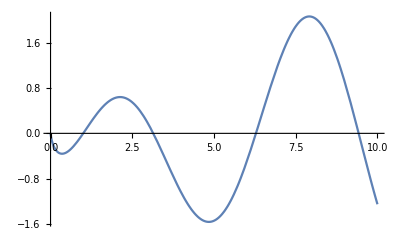

```mathematica
Plot[Log[x]Sin[x],{x,0,10}]
```

```mathematica
({x[t]->t/2+C[1],y[t]->-t/2+C[2]}/.{C[1]->1,C[2]->0})
```

{x[t]→1+t/2,y[t]→-t/2}

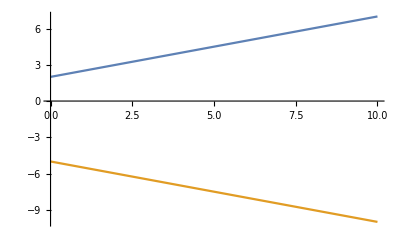

```mathematica
Plot[{t/2+2,-t/2-5},{t,0,10}]
```

Aquí viene lo de ahuevo con hacer gráficas en Mathematica:

```mathematica
Manipulate[Plot[Log[x]Sin[a x],{x,0,50}],{a,0.01,1}]
```

#### Arreglos de datos: listas

Con las listas ya podemos crear matrices. Entonces veamos algunas funciones para crear matrices, manipularlas y de álgebra lineal:

```mathematica
{1,2,3,4,5,6,7}
```

{1,2,3,4,5,6,7}

```mathematica
Range[15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
ConstantArray[1,{15}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
SparseArray[{{1,1},{1,4},{4,1},{4,4}}->{1,1,1,1},{4,4}]//Normal//MatrixForm
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

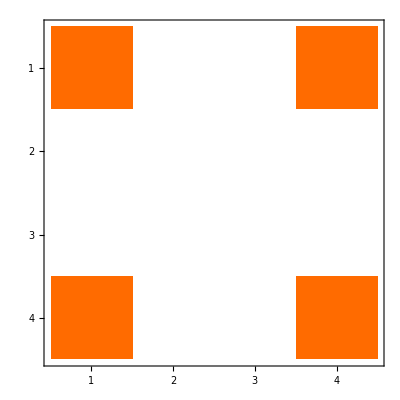

```mathematica
SparseArray[{{1,1},{1,4},{4,1},{4,4}}->{1,1,1,1},{4,4}]//Normal//MatrixPlot
```

```mathematica
(M=SparseArray[{{1,1},{1,4},{4,1},{4,4}}->{1,1,1,1},{4,4}]//Normal)//MatrixForm
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
M//MatrixForm
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

Para ‘aplastar’ una matriz:

```mathematica
M//Flatten
```

{1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1}

Para ‘reordenar’ una lista:

```mathematica
ArrayReshape[Range[16],{4,4}]//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

```mathematica
DiagonalMatrix[{1,2,3,4,5,6,7,8}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8)

Para calcular eigenvalores:

```mathematica
SeedRandom[12342];
(M2=ArrayReshape[RandomSample[Range[16]],{4,4}])//MatrixForm
```

(14 | 5 | 8 | 7
2 | 1 | 10 | 6
12 | 3 | 4 | 11
13 | 16 | 9 | 15)

```mathematica
SeedRandom[12342];
ArrayReshape[RandomSample[Range[16]],{4,4}]//Eigenvalues
```

{Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212,Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129,Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129,Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142}

```mathematica
SeedRandom[12342];
ArrayReshape[RandomSample[Range[16]],{4,4}]//Eigenvectors
```

{{(-2172326-271875 Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212-55777 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^2+1914 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^3)/5520374,(-2208874+698480 Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212+1621 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^2-501 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^3)/5520374,(-2135932-235659 Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212+77685 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^2-1874 (Root35.5Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,2]35.53022550339212)^3)/5520374,1},{(-2172326-271875 Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129-55777 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^2+1914 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^3)/5520374,(-2208874+698480 Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129+1621 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^2-501 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^3)/5520374,(-2135932-235659 Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129+77685 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^2-1874 (Root-4.05+5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,4]-4.049086671294129)^3)/5520374,1},{(-2172326-271875 Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129-55777 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^2+1914 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^3)/5520374,(-2208874+698480 Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129+1621 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^2-501 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^3)/5520374,(-2135932-235659 Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129+77685 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^2-1874 (Root-4.05-5.31 ⅈRoot[10398+14 #1-63 #1^2-34 #1^3+#1^4&,3]-4.049086671294129)^3)/5520374,1},{(-2172326-271875 Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142-55777 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^2+1914 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^3)/5520374,(-2208874+698480 Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142+1621 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^2-501 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^3)/5520374,(-2135932-235659 Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142+77685 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^2-1874 (Root6.57Root[10398+14 #1-63 #1^2-34 #1^3+#1^4&,1]6.567947839196142)^3)/5520374,1}}

```mathematica
Tr[M2]
```

34

```mathematica
ConjugateTranspose[M2]//MatrixForm
```

(14 | 2 | 12 | 13
5 | 1 | 3 | 16
8 | 10 | 4 | 9
7 | 6 | 11 | 15)

```mathematica
PauliMatrix[2]//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
KroneckerProduct[M,M2]//MatrixForm
```

(14 | 5 | 8 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 5 | 8 | 7
2 | 1 | 10 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 10 | 6
12 | 3 | 4 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 3 | 4 | 11
13 | 16 | 9 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 16 | 9 | 15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14 | 5 | 8 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 5 | 8 | 7
2 | 1 | 10 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 10 | 6
12 | 3 | 4 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 3 | 4 | 11
13 | 16 | 9 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 16 | 9 | 15)

```mathematica
M.IdentityMatrix[4]//MatrixForm
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
Det[M]
```

0

## Tarea:

En un cuaderno de Mathematica haga los siguientes ejercicios. Ponga el enunciado y explique más o menos lo que está haciendo mientras ejecuta código, como si estuviera resolviendo a lápiz y papel en un examen, con la diferencia que esto no vale puntos y sólo lo está haciendo porque es un entusiasta de la programación.

1. Repetir el ejercicio 1 de la tarea de la clase 9: calcular de nuevo las r_ijde las matrices de densidad ρ_1 y ρ_2 de esa tarea.
2. Determine la positividad de la matriz A del ejercicio 2 de la tarea de la clase 9 utilizando el criterio de eigenvalores.
2. Resolver el sistema de ecuaciones {ax+3y=5, x-ay=b} y graficar ambas ecuaciones para ver la solución gráficamente. Utilice la función Manipulate[].
3. Calcule el valor de las 3 integrales que se calcularon con el método del trapecio en las notas de clase del día 3.